## Andrea Halenkamp

#### Part 1: #1-6, 9, 10

Find the general solution

1. x’’+ 5x’ + 6x = 0

```mathematica
Solve[r^2+5r+6==0,r]
```

{{r→-3},{r→-2}}

```mathematica
DSolve[x''[t]+5*x'[t]+6x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(-3 t) C[1]+ⅇ^(-2 t) C[2]}}

2. 2x’’ + 7x’ + 3x = 0

```mathematica
Solve[2r^2+5r+6==0,r]
```

{{r→1/4 (-5-ⅈ √23)},{r→1/4 (-5+ⅈ √23)}}

```mathematica
DSolve[2*x''[t]+7*x'[t]+3*x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(-t/2) C[1]+ⅇ^(-3 t) C[2]}}

3. x’’ + 6x’ + 9x = 0

```mathematica
Solve[r^2+6r+9==0]
```

{{r→-3},{r→-3}}

```mathematica
DSolve[x''[t]+6*x'[t]+9*x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(-3 t) C[1]+ⅇ^(-3 t) t C[2]}}

4. x’’ - 9x = 0

```mathematica
Solve[r^2-9==0,r]
```

{{r→-3},{r→3}}

```mathematica
DSolve[x''[t]-9*x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(3 t) C[1]+ⅇ^(-3 t) C[2]}}

5. x’’ + 4x’ + 5x = 0

```mathematica
Solve[r^2+4r+5==0,r]
```

{{r→-2-ⅈ},{r→-2+ⅈ}}

```mathematica
DSolve[x''[t]+4*x'[t]+5*x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(-2 t) C[2] Cos[t]+ⅇ^(-2 t) C[1] Sin[t]}}

6. x’’ + x’ + x = 0

```mathematica
Solve[r^2+r+1==0,r]
```

{{r→-(-1)^(1/3)},{r→(-1)^(2/3)}}

```mathematica
DSolve[x''[t]+x'[t]+x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(-t/2) C[2] Cos[(√3 t)/2]+ⅇ^(-t/2) C[1] Sin[(√3 t)/2]}}

Find the solution and graph it on the interval 0 <= t <= 10
9. x’’ + 4x’ + 4x = 0, x(0) = 2, x’(0) = -1

```mathematica
DSolve[{x''[t]+4*x'[t]+4*x[t]==0,x[0]==2,x'[0]==-1},x[t],t]
```

{{x[t]→ⅇ^(-2 t) (2+3 t)}}

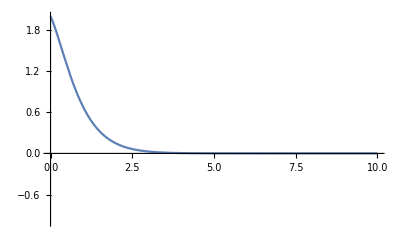

```mathematica
Plot[ⅇ^(-2 t) (2+3 t),{t,0,10},AxesOrigin->{0,0},PlotRange->{-1,2}]
```

10. x’’ + 6x’ + 7x = 0, x(0) = 0, x’(0) = 1

```mathematica
DSolve[{x''[t]+6*x'[t]+7*x[t]==0,x[0]==0,x'[0]==1},x[t],t]
```

{{x[t]→-(ⅇ^((-3-√2) t)-ⅇ^((-3+√2) t))/(2 √2)}}

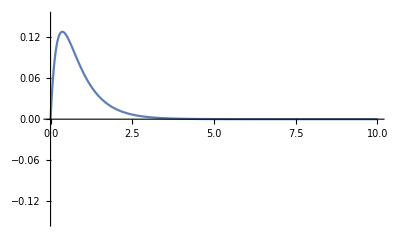

```mathematica
Plot[-(ⅇ^((-3-√2) t)-ⅇ^((-3+√2) t))/(2 √2),{t,0,10},AxesOrigin->{0,0},PlotRange->{-0.15,0.15}]
```

```mathematica
Limit[-(ⅇ^((-3-√2) t)-ⅇ^((-3+√2) t))/(2 √2),t->Infinity]
```

0